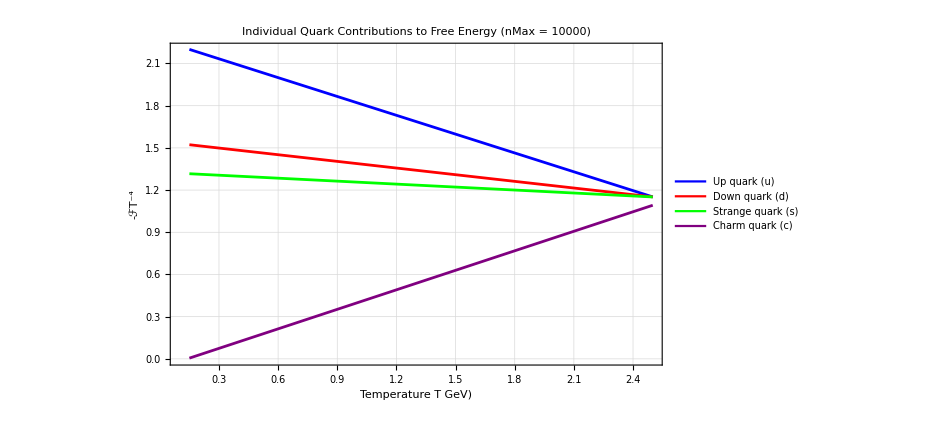

QuarkFreeEnergy_IndividualContributions_nMax10.pdf

```mathematica
(*-------------------------------------------------------*)
(*Quark-Gluon Plasma Free Energy Calculation in B Field*)
(*Individual Quark Contributions with Discrete Temperature Points*)
(*Summations Performed Inside the Integrand Before NIntegrate*)
(*Incorporates,Absolute Charges,and Charm Quark*)
(*-------------------------------------------------------*)
(*Clear previous definitions*)
ClearAll["Global`*"]

(*-------------------*)
(*Define Constants*)
(*-------------------*)
(*Number of colors*)
Nc=3; 
(*Volume of the homogeneous domain,in appropriate units*)
V=1.0;
(*Magnetic field magnitude,in GeV^2*)
B=2.5*10^(-7);
B=2.5*10^(-1);

(*--------------------------*)
(*Define Quark Properties*)
(*--------------------------*)
quarks={"u","d","s","c"}; (*Up,Down,Strange,Charm quarks*)

(*Charges in units of|e|*)
charges=<|"u"->2/3,"d"->-1/3,"s"->-1/3,"c"->2/3|>;

(*g-factors*)
gFactors=<|"u"->2,"d"->2,"s"->2,"c"->2|>;

(*Masses in GeV*)
masses=<|"u"->0.0022,"d"->0.0047,"s"->0.096,"c"->1.27|>;

(*-----------------------------------*)
(*Define Energy Eigenvalue Function*)
(*Charges are now taken as absolute values*)
(*-----------------------------------*)
energyEigenvalue[s_,n_,q_,pz_]:=Sqrt[masses[q]^2+pz^2+2 Abs[charges[q]] B (n+1/2-(gFactors[q]/2) s)];

(*-----------------------------------*)
(*Define Summation Function Inside Integrand*)
(*Charges are now taken as absolute values*)
(*-----------------------------------*)
sumLogPerQuark[T_,nMax_,pz_,q_]:=Abs[charges[q]]*Sum[Sum[Log[1+Exp[-energyEigenvalue[s,n,q,pz]/T]],{n,0,nMax}],{s,{-1/2,1/2}}];

(*-----------------------------------*)
(*Compute the Log Partition Function for a Single Quark*)
(*lnZQuark depends on T,nMax,and q*)
(*-----------------------------------*)
lnZQuark[T_,nMax_,q_]:=(Nc*V*B)/(2 Pi)^2*2*NIntegrate[sumLogPerQuark[T,nMax,pz,q],{pz,-Infinity,Infinity},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->6,PrecisionGoal->6];

(*-----------------------------------*)
(*Define the Free Energy Function for a Single Quark*)
(*FreeEnergyQuark depends on T,nMax,and q*)
(*-----------------------------------*)
FreeEnergyQuark[T_,nMax_,q_]:=-T*lnZQuark[T,nMax,q];

(*-----------------------------------*)
(*Define Temperature Points*)
(*10 points between T=0.15-2.5 GeV*)
(*-----------------------------------*)
temperatureMin=0.15;
temperatureMax=2.50;
numPoints=2;
nMax = 10^(4);
temperatures=N@Table[temperatureMin+(temperatureMax-temperatureMin) (i-1)/(numPoints-1),{i,1,numPoints}];

(*-----------------------------------*)
(*Compute Free Energy Data for Each Quark*)
(*This might take some time depending on computational resources*)
(*-----------------------------------*)
dataU=Table[{T,-T^(-4)*FreeEnergyQuark[T,nMax,"u"]},{T,temperatures}];
dataD=Table[{T,-T^(-4)*FreeEnergyQuark[T,nMax,"d"]},{T,temperatures}];
dataS=Table[{T,-T^(-4)*FreeEnergyQuark[T,nMax,"s"]},{T,temperatures}];
dataC=Table[{T,-T^(-4)*FreeEnergyQuark[T,nMax,"c"]},{T,temperatures}];

(*-----------------------------------*)
(*Define Plot Styling Options*)
(*-----------------------------------*)
labelStyle={FontFamily->"Arial",FontSize->14};

frameStyle=Directive[Black,Thick];
gridLineStyle=Directive[Gray,Dashed,Thin];

(*Define a color palette for different quarks*)
quarkColors=<|"u"->Blue,"d"->Red,"s"->Green,"c"->Purple|>;

(*Define legends corresponding to each quark*)
legends={"Up quark (u)","Down quark (d)","Strange quark (s)","Charm quark (c)"};

(*-----------------------------------*)
(*Generate the Plot with Individual Quark Contributions*)
(*-----------------------------------*)
freeEnergyPlotIndividual=ListLinePlot[
{dataU,dataD,dataS,dataC},
PlotStyle->{
quarkColors["u"],
quarkColors["d"],
quarkColors["s"],
quarkColors["c"]},
Frame->True,FrameLabel->{
Style[Row[{"Temperature ",Style["T",FontWeight->Bold]," GeV)"}],labelStyle],Style[Row[{Style["-ℱ",FontWeight->Bold],Superscript[Style["T",FontWeight->Bold],-4]}],labelStyle]},
PlotLabel->Style[Row[{"Individual Quark Contributions to Free Energy (nMax = ",ToString[nMax],")"}],labelStyle],
FrameStyle->frameStyle,GridLines->Automatic,
GridLinesStyle->gridLineStyle,LabelStyle->labelStyle,
ImageSize->700,PlotRange->All,
BaseStyle->{FontFamily->"Arial",FontSize->14},
PlotTheme->"Detailed",
PlotLegends->Placed[LineLegend[
{quarkColors["u"],
quarkColors["d"],
quarkColors["s"],
quarkColors["c"]},legends],Below],
Joined->True,(*Ensures lines are connected*)
Mesh->None (*Removes any mesh points,ensuring only lines are displayed*)
];

(*Display the individual quark contributions plot*)
freeEnergyPlotIndividual

(*-----------------------------------*)
(*Export the Plot for Publication*)
(*-----------------------------------*)
(*Export the individual quark contributions plot as PDF*)
Export["QuarkFreeEnergy_IndividualContributions_nMax10.pdf",freeEnergyPlotIndividual]

(*Alternatively,export as PNG with high resolution*)
(*Export["QuarkFreeEnergy_IndividualContributions_nMax10.png",freeEnergyPlotIndividual,ImageResolution->300]*)
```